# Parallelized ICS Interaction Optimisation + Tuning Curves

## Units, Constants, Cases + Optimisation Parameters

```mathematica
(*Units*)
```

```mathematica
MeV=10^6;
nm=10^-9;
mm=10^-3;
mrad=10^-3;
μrad=10^-6;
nrad=10^-9;
μm=10^-6;
pC=10^-12;
nC=10^-9;
μJ=10^-6;
MHz=10^6;
ps=10^-12;
```

```mathematica
(*Constants*)
```

```mathematica
me=0.51099895MeV;
h=4.135667696*10^-15; (*in eV*)
clight=299792458;
echarge=1.60217662*10^-19;
σT=6.6524587158*10^-29;
fivedeg=(5*π)/180;
```

```mathematica
(*Cases*)
```

```mathematica
CBETA150 = {Ee->150MeV,λ->1064nm,ϵn->0.3mm mrad,ϕ->fivedeg,σL->25μm,Q->32pC,Epulse->62μJ,f->162.5MHz,tpulse->10ps,σze->1mm,ΔEe->5*10^-4,Δλ->6.57*10^-4};
CBETA114 = {Ee->114MeV,λ->1064nm,ϵn->0.3mm mrad,ϕ->fivedeg,σL->25μm,Q->32pC,Epulse->62μJ,f->162.5MHz,tpulse->10ps,σze->1mm,ΔEe->5*10^-4,Δλ->6.57*10^-4};
CBETA78 = {Ee->78MeV,λ->1064nm,ϵn->0.3mm mrad,ϕ->fivedeg,σL->25μm,Q->32pC,Epulse->62μJ,f->162.5MHz,tpulse->10ps,σze->1mm,ΔEe->5*10^-4,Δλ->6.57*10^-4};
CBETA42 = {Ee->42MeV,λ->1064nm,ϵn->0.3mm mrad,ϕ->fivedeg,σL->25μm,Q->32pC,Epulse->62μJ,f->162.5MHz,tpulse->10ps,σze->1mm,ΔEe->5*10^-4,Δλ->6.57*10^-4};

DIANA340={Ee->340MeV,λ->1064nm,ϕ->fivedeg,Q->100pC,Epulse->100μJ,ϵn->0.5mm mrad,σL->25 μm,tpulse->5.7ps,σze->1mm,f->100MHz,ΔEe->5*10^-4,Δλ->6.57*10^-4};
DIANA680={Ee->680MeV,λ->1064nm,ϕ->fivedeg,Q->100pC,Epulse->100μJ,ϵn->0.5mm mrad,σL->25 μm,tpulse->5.7ps,σze->1mm,f->100MHz,ΔEe->5*10^-4,Δλ->6.57*10^-4};
DIANA1020={Ee->1020MeV,λ->1064nm,ϕ->fivedeg,Q->100pC,Epulse->100μJ,ϵn->0.5mm mrad,σL->25 μm,tpulse->5.7ps,σze->1mm,f->100MHz,ΔEe->5*10^-4,Δλ->6.57*10^-4};

(*Assuming a 7 MeV injection energy and 15 MV/m accelerating voltage*) 
DIANA347={Ee->347MeV,λ->1064nm,ϕ->fivedeg,Q->100pC,Epulse->100μJ,ϵn->0.5mm mrad,σL->25 μm,tpulse->5.7ps,σze->1mm,f->100MHz,ΔEe->5*10^-4,Δλ->6.57*10^-4};
DIANA687={Ee->687MeV,λ->1064nm,ϕ->fivedeg,Q->100pC,Epulse->100μJ,ϵn->0.5mm mrad,σL->25 μm,tpulse->5.7ps,σze->1mm,f->100MHz,ΔEe->5*10^-4,Δλ->6.57*10^-4};
DIANA1027={Ee->1027MeV,λ->1064nm,ϕ->fivedeg,Q->100pC,Epulse->100μJ,ϵn->0.5mm mrad,σL->25 μm,tpulse->5.7ps,σze->1mm,f->100MHz,ΔEe->5*10^-4,Δλ->6.57*10^-4};

(*Assuming a 7 MeV injection energy and 30 MV/m accelerating voltage*) 
DIANA687={Ee->687MeV,λ->1064nm,ϕ->fivedeg,Q->100pC,Epulse->100μJ,ϵn->0.5mm mrad,σL->25 μm,tpulse->5.7ps,σze->1mm,f->100MHz,ΔEe->5*10^-4,Δλ->6.57*10^-4};
DIANA1367={Ee->1367MeV,λ->1064nm,ϕ->fivedeg,Q->100pC,Epulse->100μJ,ϵn->0.5mm mrad,σL->25 μm,tpulse->5.7ps,σze->1mm,f->100MHz,ΔEe->5*10^-4,Δλ->6.57*10^-4};
DIANA2047={Ee->2047MeV,λ->1064nm,ϕ->fivedeg,Q->100pC,Epulse->100μJ,ϵn->0.5mm mrad,σL->25 μm,tpulse->5.7ps,σze->1mm,f->100MHz,ΔEe->5*10^-4,Δλ->6.57*10^-4};

(*Assuming a 7 MeV injection energy and 15 MV/m accelerating volatage, with a 2nd Harmonic Nd:YAG laser*)
DIANA347H2={Ee->347MeV,λ->532nm,ϕ->fivedeg,Q->100pC,Epulse->100μJ,ϵn->0.5mm mrad,σL->25 μm,tpulse->5.7ps,σze->1mm,f->100MHz,ΔEe->5*10^-4,Δλ->6.57*10^-4};
DIANA687H2={Ee->687MeV,λ->532nm,ϕ->fivedeg,Q->100pC,Epulse->100μJ,ϵn->0.5mm mrad,σL->25 μm,tpulse->5.7ps,σze->1mm,f->100MHz,ΔEe->5*10^-4,Δλ->6.57*10^-4};
DIANA1027H2={Ee->1027MeV,λ->532nm,ϕ->fivedeg,Q->100pC,Epulse->100μJ,ϵn->0.5mm mrad,σL->25 μm,tpulse->5.7ps,σze->1mm,f->100MHz,ΔEe->5*10^-4,Δλ->6.57*10^-4};

(*Assuming a 7 MeV injection energy and 22.24 MV/m accelerating volatage, with a 2nd Harmonic Nd:YAG laser*)
DIANA511={Ee->511MeV,λ->1064nm,ϕ->fivedeg,Q->100pC,Epulse->100μJ,ϵn->0.5mm mrad,σL->25 μm,tpulse->5.7ps,σze->1mm,f->100MHz,ΔEe->5*10^-4,Δλ->6.57*10^-4};
DIANA1015={Ee->1015MeV,λ->1064nm,ϕ->fivedeg,Q->100pC,Epulse->100μJ,ϵn->0.5mm mrad,σL->25 μm,tpulse->5.7ps,σze->1mm,f->100MHz,ΔEe->5*10^-4,Δλ->6.57*10^-4};
DIANA1519={Ee->1519MeV,λ->1064nm,ϕ->fivedeg,Q->100pC,Epulse->100μJ,ϵn->0.5mm mrad,σL->25 μm,tpulse->5.7ps,σze->1mm,f->100MHz,ΔEe->5*10^-4,Δλ->6.57*10^-4};

MAXIIIeq={Ee->700MeV,λ->1064nm,ϕ->fivedeg,Q->0.996nC,Epulse->120μJ,ϵn->17.5471mm mrad,σL->25μm,tpulse->5.7ps,σze->0.0266815,f->83.33MHz,ΔEe->8.6*10^-4,Δλ->6.57*10^-4};
MAXIIIinj={Ee->700MeV,λ->1064nm,ϕ->fivedeg,Q->0.996nC,Epulse->120μJ,ϵn->1.398mm mrad,σL->25μm,tpulse->5.7ps,σze->0.0266815,f->83.33MHz,ΔEe->8.6*10^-4,Δλ->6.57*10^-4};
MAXIIIinjheadon={Ee->700MeV,λ->1064nm,ϕ->0,Q->0.996nC,Epulse->120μJ,ϵn->1.398mm mrad,σL->25μm,tpulse->5.7ps,σze->0.0266815,f->83.33MHz,ΔEe->8.6*10^-4,Δλ->6.57*10^-4};
```

```mathematica
trialcase=CBETA42;
```

## Intermediaries

```mathematica
γ[Ee_]:=(Ee+me)/me;
EL[λ_]:=(h*clight)/λ;
Xrec[Ee_,λ_]:=(4*γ[Ee]*EL[λ])/me;
ψ[Ee_,θ_]:=γ[Ee]*θ;
```

## Bandwidth Terms

```mathematica
collterm[Ee_,λ_,θ_]:=1/Sqrt[12]*ψ[Ee,θ]^2/(1+Xrec[Ee,λ]+ψ[Ee,θ]^2/2);
beamspreadterm[Ee_,λ_,ΔEe_,θ_]:=(2+Xrec[Ee,λ])/(1+Xrec[Ee,λ]+ψ[Ee,θ]^2)*ΔEe;
laserspreadterm[Ee_,λ_,Δλ_,θ_]:=(1+ψ[Ee,θ]^2)/(1+Xrec[Ee,λ]+ψ[Ee,θ]^2)*Δλ;
```

## Flux Intermediaries

```mathematica
σc[Ee_,λ_]:=σT*(1-Xrec[Ee,λ]);
Ne[Q_]:=Q/echarge;
NL[Epulse_,λ_]:=Epulse/(echarge*EL[λ]);
σe[βIP_,ϵn_,Ee_]:=Sqrt[(βIP*ϵn)/γ[Ee]];
σzl[tpulse_]:=clight*tpulse;
convxy[βIP_,ϵn_,Ee_,σL_]:=Sqrt[σe[βIP,ϵn,Ee]^2+σL^2];
convz[σze_,tpulse_]:=Sqrt[σze^2+σzl[tpulse]^2];
```

## β^* Calculation

```mathematica
βstar[Ee_,ϵn_,BW_,λ_,ΔEe_,Δλ_,θ_]:=(2*γ[Ee]*ϵn)/((1+Xrec[Ee,λ])*Sqrt[BW^2-(collterm[Ee,λ,θ]^2+beamspreadterm[Ee,λ,ΔEe,θ]^2+laserspreadterm[Ee,λ,Δλ,θ]^2)]);
```

## Uncollimated Flux Calculation

```mathematica
F[Ee_,λ_,Q_,Epulse_,f_,ϕ_,βIP_,ϵn_,σL_,σze_,tpulse_]:=σc[Ee,λ]*(Ne[Q]*NL[Epulse,λ]*f*Cos[ϕ/2])/(2*π*convxy[βIP,ϵn,Ee,σL]*Sqrt[convxy[βIP,ϵn,Ee,σL]^2*Cos[ϕ/2]^2+convz[σze,tpulse]^2*Sin[ϕ/2]^2]);
```

## Collimated Flux Calculation

```mathematica
Fψ[Ee_,λ_,Q_,Epulse_,f_,ϕ_,βIP_,ϵn_,σL_,σze_,tpulse_,θ_]:=Sqrt[2]/π*F[Ee,λ,Q,Epulse,f,ϕ,βIP,ϵn,σL,σze,tpulse]*((1+(CubeRoot[Xrec[Ee,λ]]*ψ[Ee,θ]^2)/3)*ψ[Ee,θ]^2)/((1+(1+Xrec[Ee,λ]/2)*ψ[Ee,θ]^2)*(1+ψ[Ee,θ]^2));
```

# Single Fixed Bandwidth Optimisation

```mathematica
(*Optimisation Parameters*)
BW=0.5/100;
θmax=5mrad;
θstep=10nrad;(*μrad typically used for tuning curves, 10 nrad used for single cases*)
```

## β^*-θ_col Pairings

```mathematica
βstardat=Table[{θ,Re[βstar[Ee,ϵn,BW,λ,ΔEe,Δλ,θ]]/.trialcase},{θ,0,θmax,θstep}]//AbsoluteTiming;
simtime={βstardat⟦1⟧};
```

```mathematica
imaginarycut=Min[Position[βstardat⟦2⟧⟦All,2⟧,0.]]//AbsoluteTiming;
AppendTo[simtime,imaginarycut⟦1⟧];
```

```mathematica
βstardat=βstardat⟦2⟧⟦1;;(imaginarycut⟦2⟧-1),All⟧//AbsoluteTiming;
AppendTo[simtime,βstardat⟦1⟧];
```

β^*is calculated for each step in the range 0 to θmax. The position at which β^* becomes imaginary is found and then the imaginary values are discarded.

## Collimated Flux Maximisation

```mathematica
Fψdat=Table[{βstardat⟦2⟧⟦i,1⟧,βstardat⟦2⟧⟦i,2⟧,Fψ[Ee,λ,Q,Epulse,f,ϕ,βstardat⟦2⟧⟦i,2⟧,ϵn,σL,σze,tpulse,βstardat⟦2⟧⟦i,1⟧]/.trialcase},{i,1,(imaginarycut⟦2⟧-1),1}]//AbsoluteTiming;
AppendTo[simtime,Fψdat⟦1⟧];
```

```mathematica
maxval=Position[Fψdat⟦2⟧⟦All,3⟧,Max[Fψdat⟦2⟧⟦All,3⟧]]⟦1,1⟧;
```

```mathematica
(Fψdat⟦2⟧⟦maxval,1⟧)/mrad//N
Fψdat⟦2⟧⟦maxval,2⟧
Fψdat⟦2⟧⟦maxval,3⟧
```

0.08656

1.58586

3.8826×10^8

```mathematica
Total[simtime]
```

108.848

# Tuning Curve Optimisation

```mathematica
(*Optimisation Parameters*)
BWmin=Sqrt[(2*ΔEe/.trialcase)^2+(Δλ/.trialcase)^2]; 
BWmax=1/100;
BWstep=10^-3/100;
θmax=3mrad;
θstep=0.2μrad;(*μrad typically used for tuning curves, 10 nrad used for single cases*)
```

## β^*-θ_col Pairings

Nested computations like nested tables can’t both be parallelized. Therefore, only the inner table (the more computationally intensive) is parallelized.

```mathematica
LaunchKernels[10];
```

```mathematica
DistributeDefinitions[βstar,BWmin,BWmax,BWstep,θmax,θstep,Fψ];
```

```mathematica
βstardatcurve=Table[{BW,ParallelTable[{θ,Re[βstar[Ee,ϵn,BW,λ,ΔEe,Δλ,θ]]/.trialcase},{θ,0,θmax,θstep}]},{BW,BWmin,BWmax,BWstep}]//AbsoluteTiming;
```

```mathematica
simtime={βstardatcurve⟦1⟧};
```

```mathematica
CloseKernels[];
```

```mathematica
imaginarycuts=Table[Min[Position[βstardatcurve⟦2⟧⟦i,2⟧⟦All,2⟧,0.]],{i,1,((BWmax-BWmin)/BWstep)}]//AbsoluteTiming;
AppendTo[simtime,imaginarycuts⟦1⟧];
```

```mathematica
βstardatcurve=Table[{βstardatcurve⟦2⟧⟦i,1⟧,βstardatcurve⟦2⟧⟦i,2⟧⟦1;;(imaginarycuts⟦2⟧⟦i⟧-1),All⟧},{i,1,((BWmax-BWmin)/BWstep)}]//AbsoluteTiming;
AppendTo[simtime,βstardatcurve⟦1⟧];
```

## Collimated Flux Maximisation

```mathematica
LaunchKernels[10];
```

```mathematica
DistributeDefinitions[Fψ,βstardatcurve,imaginarycuts,BWmax,BWmin,BWstep];
```

```mathematica
Fψdatcurve=Table[{βstardatcurve⟦2⟧⟦i,1⟧,ParallelTable[{βstardatcurve⟦2⟧⟦i,2⟧⟦j,1⟧,βstardatcurve⟦2⟧⟦i,2⟧⟦j,2⟧,Fψ[Ee,λ,Q,Epulse,f,ϕ,βstardatcurve⟦2⟧⟦i,2⟧⟦j,2⟧,ϵn,σL,σze,tpulse,βstardatcurve⟦2⟧⟦i,2⟧⟦j,1⟧]/.trialcase},{j,1,(imaginarycuts⟦2⟧⟦i⟧-1)}]},{i,1,((BWmax-BWmin)/BWstep)}]//AbsoluteTiming;
```

```mathematica
AppendTo[simtime,Fψdatcurve⟦1⟧];
```

```mathematica
CloseKernels[];
```

```mathematica
maxvals=Table[Position[Fψdatcurve⟦2⟧⟦i,2⟧⟦All,3⟧,Max[Fψdatcurve⟦2⟧⟦i,2⟧⟦All,3⟧]]⟦1,1⟧,{i,1,((BWmax-BWmin)/BWstep)}]//AbsoluteTiming;
AppendTo[simtime,maxvals⟦1⟧];
```

```mathematica
maxdata=Table[{Fψdatcurve⟦2⟧⟦i,1⟧*100,(Fψdatcurve⟦2⟧⟦All,2⟧⟦i,maxvals⟦2⟧⟦i⟧,1⟧)/mrad,Fψdatcurve⟦2⟧⟦All,2⟧⟦i,maxvals⟦2⟧⟦i⟧,2⟧,Fψdatcurve⟦2⟧⟦All,2⟧⟦i,maxvals⟦2⟧⟦i⟧,3⟧},{i,1,((BWmax-BWmin)/BWstep)}]//AbsoluteTiming;
AppendTo[simtime,maxdata⟦1⟧];
```

The maxdata array is of the form BW, θcol, β^*, F_ψ . All of the necessary data is available in this singular array.

```mathematica
Total[simtime]/60
```

98.4822

```mathematica
simtime
```

{865.605,8.0687,5.54862,5018.18,7.70097,3.82882}

## Saving Data

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/TuningDat/CBETA"];
maxdata⟦2⟧>>"CBETA42opt.txt";
```

## Plotting Data

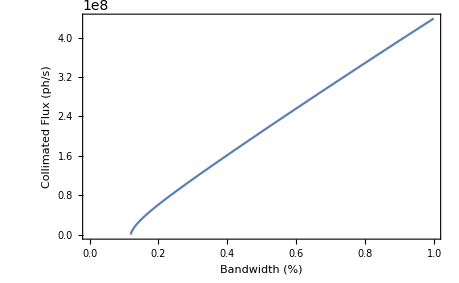

```mathematica
ListLinePlot[Partition[Riffle[maxdata⟦2⟧⟦All,1⟧,maxdata⟦2⟧⟦All,4⟧],2],Frame->True,FrameLabel->{"Bandwidth (%)","Collimated Flux (ph/s)"},LabelStyle->16]
```

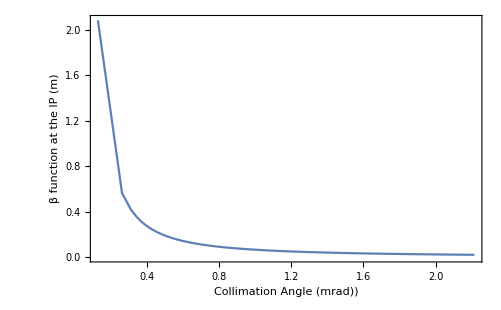

```mathematica
ListLinePlot[Partition[Riffle[maxdata⟦2⟧⟦All,2⟧,maxdata⟦2⟧⟦All,3⟧],2],Frame->True,FrameLabel->{"Collimation Angle (mrad))","β function at the IP (m)"},LabelStyle->16,PlotRange->All]
```

# Benchmarking

```mathematica
KernelvsTime={{1,5,10,15,20,25,30},{1529.30,681.59,631.78,599.68,605.57,602.04,616.32}/60};
```

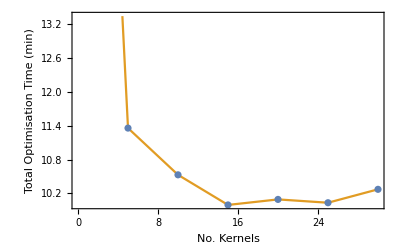

```mathematica
ListPlot[{Transpose[KernelvsTime],Transpose[KernelvsTime]},Joined->{False,True},Frame->True,LabelStyle->15,FrameLabel->{"No. Kernels","Total Optimisation Time (min)"}]
```

```mathematica
longKernelvsTime={{15},{5569.80}};
```

# Multiple Case Plotting

```mathematica
(*CBETA ICS*)
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/TuningDat/CBETA"];
optCBETA150=<<"CBETA150opt.txt";
optCBETA114=<<"CBETA114opt.txt";
optCBETA78=<<"CBETA78opt.txt";
optCBETA42=<<"CBETA42opt.txt";
```

```mathematica
(*DIANA (Older Config) vs MAXIII NEQ-SR ICS*)
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/TuningDat"];
optMAXIIIinj=<<"MAXIIIinjopt.txt";
optMAXIIIeq=<<"MAXIIIeqopt.txt";

optDIANA340=<<"DIANA340opt.txt";
optDIANA680=<<"DIANA680opt.txt";
optDIANA1020=<<"DIANA1020opt.txt";
```

```mathematica
(*DIANA Configurations*)
```

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/TuningDat/DIANA/7MeV_15MVm"];
optDIANA347=<<"DIANA347opt.txt";
optDIANA687=<<"DIANA687opt.txt";
optDIANA1027=<<"DIANA1027opt.txt";
```

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/TuningDat/DIANA/7MeV_30MVm"];
optDIANA687=<<"DIANA687opt.txt";
optDIANA1367=<<"DIANA1367opt.txt";
optDIANA2047=<<"DIANA2047opt.txt";
```

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/TuningDat/DIANA/7MeV_15MVm_2H"];
optDIANA347H2=<<"DIANA347H2opt.txt";
optDIANA687H2=<<"DIANA687H2opt.txt";
optDIANA1027H2=<<"DIANA1027H2opt.txt";
```

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/TuningDat/DIANA/7MeV_22.24MVm"];
optDIANA511=<<"DIANA511opt.txt";
optDIANA1015=<<"DIANA1015opt.txt";
optDIANA1519=<<"DIANA1519opt.txt";
```

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->Black,RoundingRadius->0,FrameMargins->0]
```

# CBETA ICS

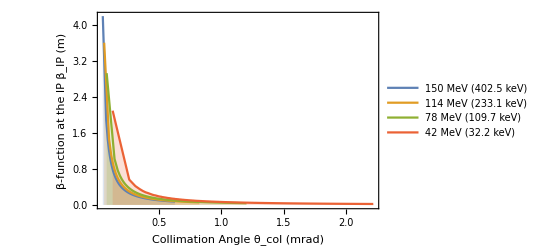

```mathematica
ListLinePlot[{Partition[Riffle[optCBETA150⟦All,2⟧,optCBETA150⟦All,3⟧],2],Partition[Riffle[optCBETA114⟦All,2⟧,optCBETA114⟦All,3⟧],2],Partition[Riffle[optCBETA78⟦All,2⟧,optCBETA78⟦All,3⟧],2],Partition[Riffle[optCBETA42⟦All,2⟧,optCBETA42⟦All,3⟧],2]},Frame->True,FrameLabel->{"Collimation Angle θ_col (mrad)","β-function at the IP β_IP (m)"},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLegends->Placed[LineLegend[{"150 MeV (402.5 keV)","114 MeV (233.1 keV)","78 MeV (109.7 keV)","42 MeV (32.2 keV)"},LabelStyle->12,LegendFunction->frame],{0.7,0.7}],PlotRange->Full,Filling->Axis]
```

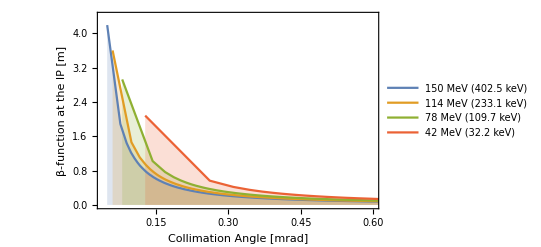

```mathematica
ListLinePlot[{Partition[Riffle[optCBETA150⟦All,2⟧,optCBETA150⟦All,3⟧],2],Partition[Riffle[optCBETA114⟦All,2⟧,optCBETA114⟦All,3⟧],2],Partition[Riffle[optCBETA78⟦All,2⟧,optCBETA78⟦All,3⟧],2],Partition[Riffle[optCBETA42⟦All,2⟧,optCBETA42⟦All,3⟧],2]},Frame->True,FrameLabel->{"Collimation Angle [mrad]","β-function at the IP [m]"},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLegends->Placed[LineLegend[{"150 MeV (402.5 keV)","114 MeV (233.1 keV)","78 MeV (109.7 keV)","42 MeV (32.2 keV)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.7,0.7}],PlotRange->{{0.04,0.6},{0,4.4}},Filling->Axis]
```

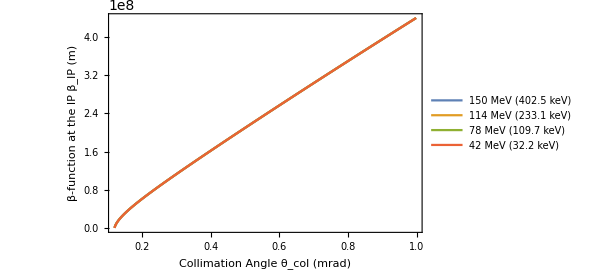

```mathematica
ListLinePlot[{Partition[Riffle[optCBETA150⟦All,1⟧,optCBETA150⟦All,4⟧],2],Partition[Riffle[optCBETA114⟦All,1⟧,optCBETA114⟦All,4⟧],2],Partition[Riffle[optCBETA78⟦All,1⟧,optCBETA78⟦All,4⟧],2],Partition[Riffle[optCBETA42⟦All,1⟧,optCBETA42⟦All,4⟧],2]},Frame->True,FrameLabel->{"Collimation Angle θ_col (mrad)","β-function at the IP β_IP (m)"},LabelStyle->15,PlotLegends->Placed[LineLegend[{"150 MeV (402.5 keV)","114 MeV (233.1 keV)","78 MeV (109.7 keV)","42 MeV (32.2 keV)"},LabelStyle->12,LegendFunction->frame],{0.75,0.25}],PlotRange->Full]
```

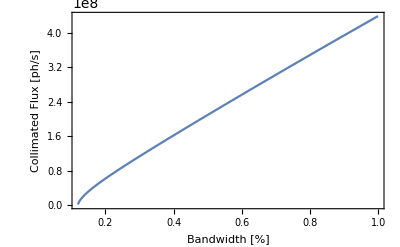

```mathematica
ListLinePlot[Partition[Riffle[optCBETA150⟦All,1⟧,optCBETA150⟦All,4⟧],2],Frame->True,FrameLabel->{"Bandwidth [%]","Collimated Flux [ph/s]"},LabelStyle->{15,,FontFamily->"Calibri",FontColor->Black},PlotRange->Full]
```

# DIANA vs MAXIII NEQ SR

## MAXIII Non-Eq ICS Plots

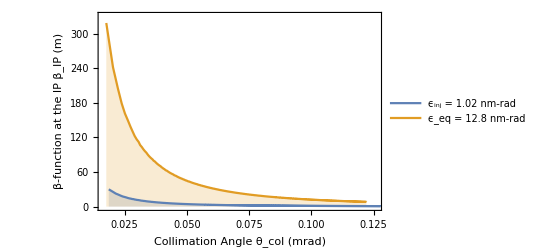

```mathematica
ListLinePlot[{Partition[Riffle[optMAXIIIinj⟦All,2⟧,optMAXIIIinj⟦All,3⟧],2],Partition[Riffle[optMAXIIIeq⟦All,2⟧,optMAXIIIeq⟦All,3⟧],2]},Frame->True,FrameLabel->{"Collimation Angle θ_col (mrad)","β-function at the IP β_IP (m)"},LabelStyle->16,PlotLegends->Placed[LineLegend[{"ϵ_inj = 1.02 nm-rad","ϵ_eq = 12.8 nm-rad"},LabelStyle->12,LegendFunction->frame],{0.7,0.7}],PlotRange->{{0.0165,0.126},{0,330}},Filling->Axis]
```

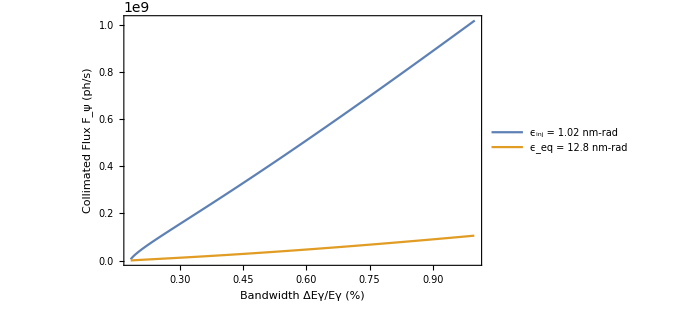

```mathematica
ListLinePlot[{Partition[Riffle[optMAXIIIinj⟦All,1⟧,optMAXIIIinj⟦All,4⟧],2],Partition[Riffle[optMAXIIIeq⟦All,1⟧,optMAXIIIeq⟦All,4⟧],2]},Frame->True,FrameLabel->{"Bandwidth ΔEγ/Eγ (%)","Collimated Flux F_ψ (ph/s)"},LabelStyle->16,PlotLegends->Placed[LineLegend[{"ϵ_inj = 1.02 nm-rad","ϵ_eq = 12.8 nm-rad"},LabelStyle->12,LegendFunction->frame],{0.2,0.7}],PlotRange->Full]
```

## DIANA Plots (No Injection)

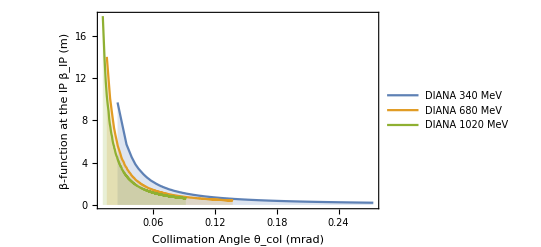

```mathematica
ListLinePlot[{Partition[Riffle[optDIANA340⟦All,2⟧,optDIANA340⟦All,3⟧],2],Partition[Riffle[optDIANA680⟦All,2⟧,optDIANA680⟦All,3⟧],2],Partition[Riffle[optDIANA1020⟦All,2⟧,optDIANA1020⟦All,3⟧],2]},Frame->True,FrameLabel->{"Collimation Angle θ_col (mrad)","β-function at the IP β_IP (m)"},LabelStyle->16,PlotLegends->Placed[LineLegend[{"DIANA 340 MeV","DIANA 680 MeV","DIANA 1020 MeV"},LabelStyle->12,LegendFunction->frame],{0.7,0.7}],PlotRange->Full,Filling->Axis]
```

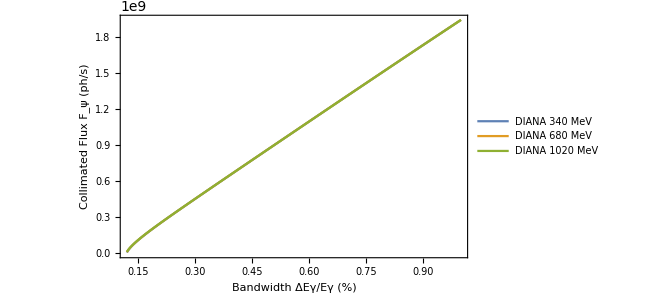

```mathematica
ListLinePlot[{Partition[Riffle[optDIANA340⟦All,1⟧,optDIANA340⟦All,4⟧],2],Partition[Riffle[optDIANA680⟦All,1⟧,optDIANA680⟦All,4⟧],2],Partition[Riffle[optDIANA1020⟦All,1⟧,optDIANA1020⟦All,4⟧],2]},Frame->True,FrameLabel->{"Bandwidth ΔEγ/Eγ (%)","Collimated Flux F_ψ (ph/s)"},LabelStyle->16,PlotLegends->Placed[LineLegend[{"DIANA 340 MeV","DIANA 680 MeV","DIANA 1020 MeV"},LabelStyle->12,LegendFunction->frame],{0.7,0.25}],PlotRange->Full]
```

## DIANA (No Injection) vs MAXIII Non-Eq Ring Plots

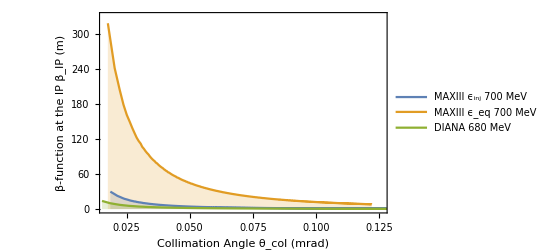

```mathematica
ListLinePlot[{Partition[Riffle[optMAXIIIinj⟦All,2⟧,optMAXIIIinj⟦All,3⟧],2],Partition[Riffle[optMAXIIIeq⟦All,2⟧,optMAXIIIeq⟦All,3⟧],2],Partition[Riffle[optDIANA680⟦All,2⟧,optDIANA680⟦All,3⟧],2]},Frame->True,FrameLabel->{"Collimation Angle θ_col (mrad)","β-function at the IP β_IP (m)"},LabelStyle->16,PlotLegends->Placed[LineLegend[{"MAXIII ϵ_inj 700 MeV","MAXIII ϵ_eq 700 MeV", "DIANA 680 MeV"},LabelStyle->12,LegendFunction->frame],{0.7,0.7}],PlotRange->{{0.0165,0.126},{0,330}},Filling->Axis]
```

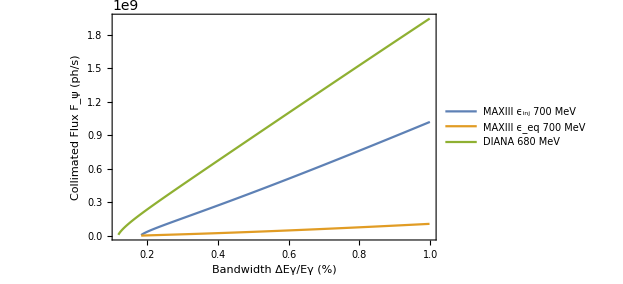

```mathematica
ListLinePlot[{Partition[Riffle[optMAXIIIinj⟦All,1⟧,optMAXIIIinj⟦All,4⟧],2],Partition[Riffle[optMAXIIIeq⟦All,1⟧,optMAXIIIeq⟦All,4⟧],2],Partition[Riffle[optDIANA680⟦All,1⟧,optDIANA680⟦All,4⟧],2]},Frame->True,FrameLabel->{"Bandwidth ΔEγ/Eγ (%)","Collimated Flux F_ψ (ph/s)"},LabelStyle->16,PlotLegends->Placed[LineLegend[{"MAXIII ϵ_inj 700 MeV","MAXIII ϵ_eq 700 MeV","DIANA 680 MeV"},LabelStyle->12,LegendFunction->frame],{0.25,0.7}],PlotRange->Full]
```

# DIANA Configurations

## DIANA (7 MeV Injection, 15MV/m Accelerating, Fundamental Harmonic)

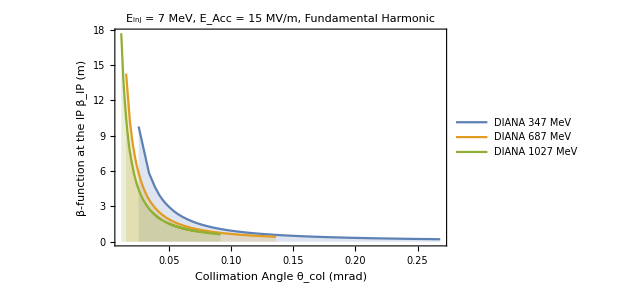

```mathematica
βθ7I15A1=ListLinePlot[{Partition[Riffle[optDIANA347⟦All,2⟧,optDIANA347⟦All,3⟧],2],Partition[Riffle[optDIANA687⟦All,2⟧,optDIANA687⟦All,3⟧],2],Partition[Riffle[optDIANA1027⟦All,2⟧,optDIANA1027⟦All,3⟧],2]},Frame->True,PlotLabel->"E_inj = 7 MeV, E_Acc = 15 MV/m, Fundamental Harmonic",FrameLabel->{"Collimation Angle θ_col (mrad)","β-function at the IP β_IP (m)"},LabelStyle->15,PlotLegends->Placed[LineLegend[{"DIANA 347 MeV","DIANA 687 MeV","DIANA 1027 MeV"},LabelStyle->12,LegendFunction->frame],{0.7,0.7}],PlotRange->Full,Filling->Axis]
```

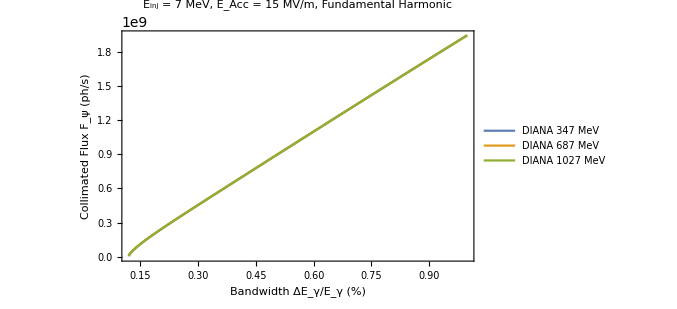

```mathematica
FBW7I15A1=ListLinePlot[{Partition[Riffle[optDIANA347⟦All,1⟧,optDIANA347⟦All,4⟧],2],Partition[Riffle[optDIANA687⟦All,1⟧,optDIANA687⟦All,4⟧],2],Partition[Riffle[optDIANA1027⟦All,1⟧,optDIANA1027⟦All,4⟧],2]},Frame->True,FrameLabel->{"Bandwidth ΔE_γ/E_γ (%)","Collimated Flux F_ψ (ph/s)"},PlotLabel->"E_inj = 7 MeV, E_Acc = 15 MV/m, Fundamental Harmonic",LabelStyle->15,PlotLegends->Placed[LineLegend[{"DIANA 347 MeV","DIANA 687 MeV","DIANA 1027 MeV"},LabelStyle->12,LegendFunction->frame],{0.7,0.25}],PlotRange->Full]
```

## DIANA (7 MeV injection, 30MV/m Accelerating, Fundamental Harmonic)

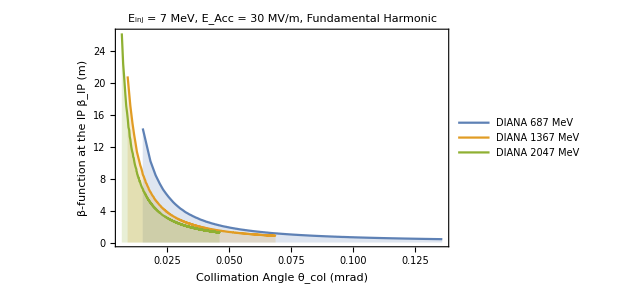

```mathematica
βθ7I30A1=ListLinePlot[{Partition[Riffle[optDIANA687⟦All,2⟧,optDIANA687⟦All,3⟧],2],Partition[Riffle[optDIANA1367⟦All,2⟧,optDIANA1367⟦All,3⟧],2],Partition[Riffle[optDIANA2047⟦All,2⟧,optDIANA2047⟦All,3⟧],2]},Frame->True,PlotLabel->"E_inj = 7 MeV, E_Acc = 30 MV/m, Fundamental Harmonic",FrameLabel->{"Collimation Angle θ_col (mrad)","β-function at the IP β_IP (m)"},LabelStyle->16,PlotLegends->Placed[LineLegend[{"DIANA 687 MeV","DIANA 1367 MeV","DIANA 2047 MeV"},LabelStyle->12,LegendFunction->frame],{0.7,0.7}],PlotRange->Full,Filling->Axis]
```

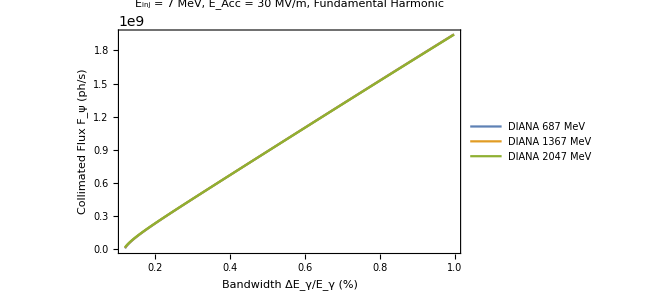

```mathematica
FBW7I30A1=ListLinePlot[{Partition[Riffle[optDIANA687⟦All,1⟧,optDIANA687⟦All,4⟧],2],Partition[Riffle[optDIANA1367⟦All,1⟧,optDIANA1367⟦All,4⟧],2],Partition[Riffle[optDIANA2047⟦All,1⟧,optDIANA2047⟦All,4⟧],2]},Frame->True,FrameLabel->{"Bandwidth ΔE_γ/E_γ (%)","Collimated Flux F_ψ (ph/s)"},PlotLabel->"E_inj = 7 MeV, E_Acc = 30 MV/m, Fundamental Harmonic",LabelStyle->15,PlotLegends->Placed[LineLegend[{"DIANA 687 MeV","DIANA 1367 MeV","DIANA 2047 MeV"},LabelStyle->12,LegendFunction->frame],{0.7,0.25}],PlotRange->Full]
```

## DIANA (7 MeV Injection, 15 MV/m Accelerating, 2nd Harmonic)

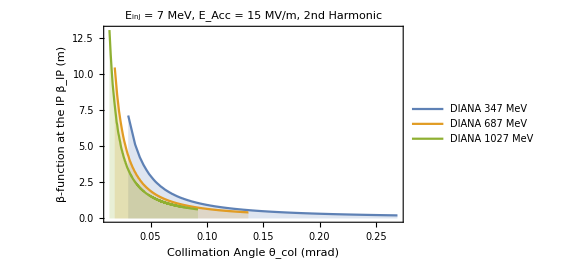

```mathematica
βθ7I15A2=ListLinePlot[{Partition[Riffle[optDIANA347H2⟦All,2⟧,optDIANA347H2⟦All,3⟧],2],Partition[Riffle[optDIANA687H2⟦All,2⟧,optDIANA687H2⟦All,3⟧],2],Partition[Riffle[optDIANA1027H2⟦All,2⟧,optDIANA1027H2⟦All,3⟧],2]},Frame->True,PlotLabel->"E_inj = 7 MeV, E_Acc = 15 MV/m, 2nd Harmonic",FrameLabel->{"Collimation Angle θ_col (mrad)","β-function at the IP β_IP (m)"},LabelStyle->16,PlotLegends->Placed[LineLegend[{"DIANA 347 MeV","DIANA 687 MeV","DIANA 1027 MeV"},LabelStyle->12,LegendFunction->frame],{0.7,0.7}],PlotRange->Full,Filling->Axis]
```

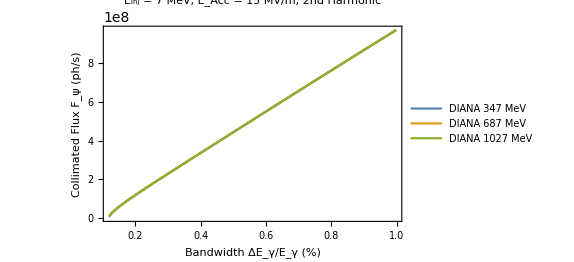

```mathematica
FBW7I15A2=ListLinePlot[{Partition[Riffle[optDIANA347H2⟦All,1⟧,optDIANA347H2⟦All,4⟧],2],Partition[Riffle[optDIANA687H2⟦All,1⟧,optDIANA687H2⟦All,4⟧],2],Partition[Riffle[optDIANA1027H2⟦All,1⟧,optDIANA1027H2⟦All,4⟧],2]},Frame->True,FrameLabel->{"Bandwidth ΔE_γ/E_γ (%)","Collimated Flux F_ψ (ph/s)"},PlotLabel->"E_inj = 7 MeV, E_Acc = 15 MV/m, 2nd Harmonic",LabelStyle->15,PlotLegends->Placed[LineLegend[{"DIANA 347 MeV","DIANA 687 MeV","DIANA 1027 MeV"},LabelStyle->12,LegendFunction->frame],{0.7,0.25}],PlotRange->Full]
```

## DIANA (7 MeV Injection, 22.24MV/m Accelerating, Fundamental Harmonic)

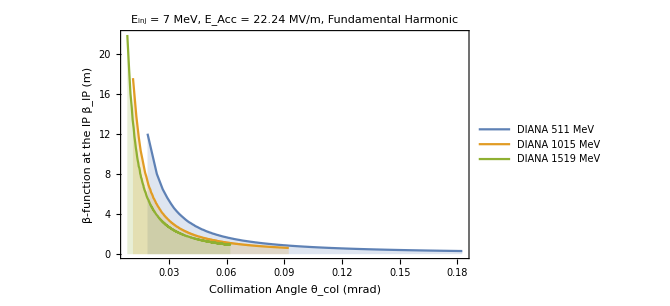

```mathematica
βθ7I22A1=ListLinePlot[{Partition[Riffle[optDIANA511⟦All,2⟧,optDIANA511⟦All,3⟧],2],Partition[Riffle[optDIANA1015⟦All,2⟧,optDIANA1015⟦All,3⟧],2],Partition[Riffle[optDIANA1519⟦All,2⟧,optDIANA1519⟦All,3⟧],2]},Frame->True,PlotLabel->"E_inj = 7 MeV, E_Acc = 22.24 MV/m, Fundamental Harmonic",FrameLabel->{"Collimation Angle θ_col (mrad)","β-function at the IP β_IP (m)"},LabelStyle->16,PlotLegends->Placed[LineLegend[{"DIANA 511 MeV","DIANA 1015 MeV","DIANA 1519 MeV"},LabelStyle->12,LegendFunction->frame],{0.7,0.7}],PlotRange->Full,Filling->Axis]
```

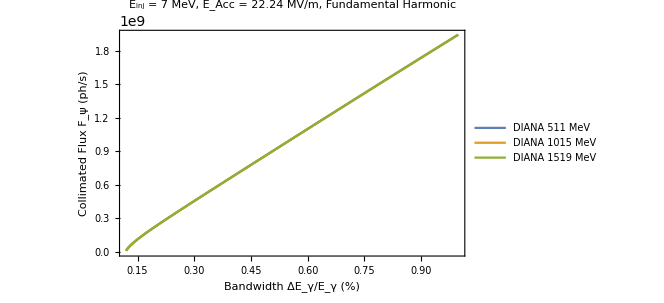

```mathematica
FBW7I22A1=ListLinePlot[{Partition[Riffle[optDIANA511⟦All,1⟧,optDIANA511⟦All,4⟧],2],Partition[Riffle[optDIANA1015⟦All,1⟧,optDIANA1015⟦All,4⟧],2],Partition[Riffle[optDIANA1519⟦All,1⟧,optDIANA1519⟦All,4⟧],2]},Frame->True,FrameLabel->{"Bandwidth ΔE_γ/E_γ (%)","Collimated Flux F_ψ (ph/s)"},PlotLabel->"E_inj = 7 MeV, E_Acc = 22.24 MV/m, Fundamental Harmonic",LabelStyle->15,PlotLegends->Placed[LineLegend[{"DIANA 511 MeV","DIANA 1015 MeV","DIANA 1519 MeV"},LabelStyle->12,LegendFunction->frame],{0.7,0.25}],PlotRange->Full]
```

## Combined Grid Plot

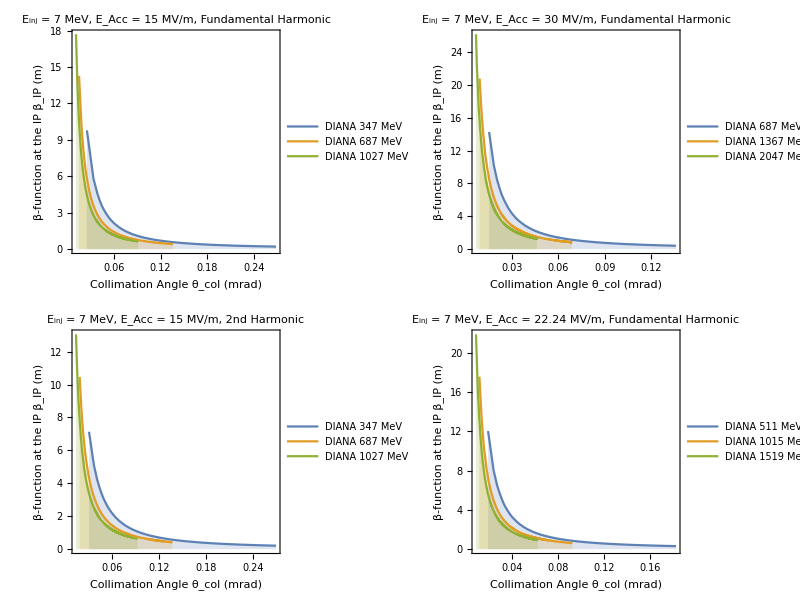

```mathematica
DIANAoptionβθ=Grid[{{βθ7I15A1,βθ7I30A1},{βθ7I15A2,βθ7I22A1}}]
```

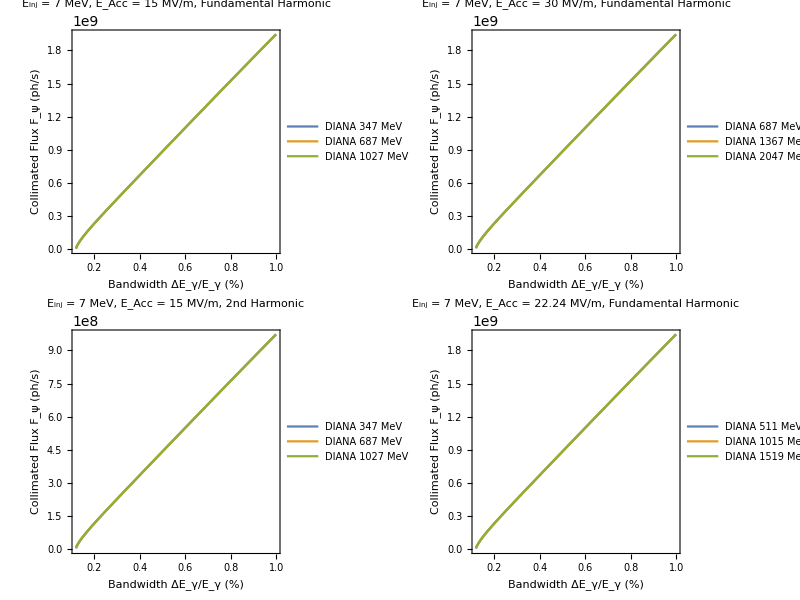

```mathematica
DIANAoptionFBW=Grid[{{FBW7I15A1,FBW7I30A1},{FBW7I15A2,FBW7I22A1}}]
```